```mathematica
Clear["Global`*"]
```

## Вычисление интегралов

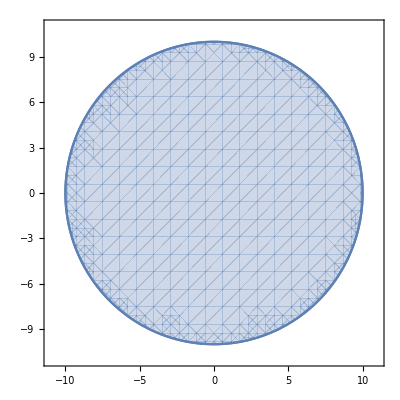

```mathematica
R=10;

Show[
ContourPlot[x^2+y^2==R^2,{x,-11,11},{y,-11,11}],
RegionPlot[x^2+y^2<=R^2,{x,-11,11},{y,-11,11}]
]
```

```mathematica
Integrate[Boole[x^2+y^2<=R^2],{x,-15,15},{y,-15,15}]
```

100 π

```mathematica
Integrate[Boole[x^2+y^2<=R^2],{x,-∞,+∞},{y,-∞,+∞}]
```

100 π

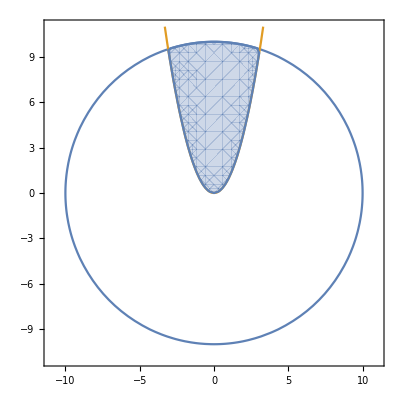

```mathematica
Show[
ContourPlot[{x^2+y^2==R^2, y-x^2==0},{x,-11,11},{y,-11,11}],
RegionPlot[{x^2+y^2<=R^2 &&y-x^2>=0},{x,-11,11},{y,-11,11}]
]
```

```mathematica
Integrate[Boole[x^2+y^2<=R^2 &&y-x^2>=0],{x,-∞,+∞},{y,-∞,+∞}]
```

1/6 (√(2 (-301+101 √401))+300 ArcSin[Root0.587Root[-400+301 #1^2+2500 #1^4&,2]0.5867748160656828])

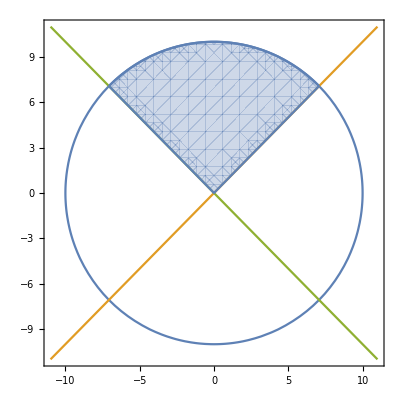

```mathematica
Show[
ContourPlot[{x^2+y^2==R^2, y==x,y==-x},{x,-11,11},{y,-11,11}],
RegionPlot[{x^2+y^2<=R^2&& y>=x &&y>=-x},{x,-11,11},{y,-11,11}]
]
```

```mathematica
Integrate[Boole[x^2+y^2<=R^2&& y>=x &&y>=-x],{x,-∞,+∞},{y,-∞,+∞}]
```

25 π

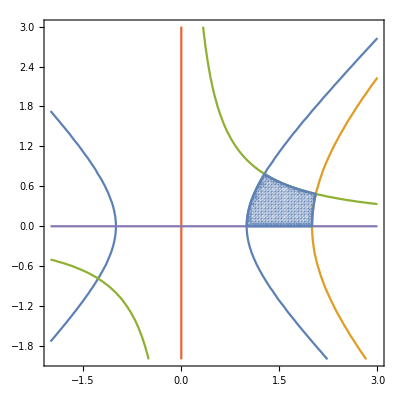

```mathematica
Show[
ContourPlot[
{x^2-y^2==1,x^2-y^2==4,x*y==1,x==0,y==0}
,{x,-2,3},{y,-2,3}
],
RegionPlot[{y>=0&&x^2-y^2>=1 && x y<=1&&x^2-y^2<=4&&x>=0},{x,-2,3},{y,-2,3}
,PlotPoints->100]
]
```

```mathematica
Integrate[Boole[y>=0&&x^2-y^2>=1 && x y<=1&&x^2-y^2<=4&&x>=0],{x,-∞,+∞},{y,-∞,+∞}]
```

1/4 (4 ArcCsch[2]+ArcSinh[2]+4 Log[2]-2 Log[4]-2 Log[1/2 (1+√5)])

```mathematica
1/4 (4 ArcCsch[2]+ArcSinh[2]+4 Log[2]-2 Log[4]-2 Log[1/2 (1+√5)])//N
```

0.601515

```mathematica
RegionPlot3D[{x^2+y^2<=z^2&& 1>=z>=0},{x,-2,2},{y,-2,2},{z,-1,2},PlotPoints->100]
```

-Graphics3D-

```mathematica
Integrate[(x^2+y^2)Boole[x^2+y^2<=z^2&& 1>=z>=0],{x,-2,2},{y,-2,2},{z,-1,2}]
```

π/10

```mathematica
Integrate[Boole[x^2+y^2<=a^2&&a>=0],{x,0,1},{y,0,1}]
```

Piecewise[{{1, a≥√2}, {(a^2 π)/4, 0<a≤1}, {1/2 (2 √(-1+a^2)+a^2 ArcCsc[a]-a^2 ArcTan[√(-1+a^2)]), 1<a<√2}, {0, True}}]

```mathematica
Integrate[Boole[x^2+y^2<=a^2],{x,0,1},{y,0,1},Assumptions->a>=0]
```

Piecewise[{{1, a≥√2}, {(a^2 π)/4, 0<a≤1}, {1/2 (2 √(-1+a^2)+a^2 ArcCsc[a]-a^2 ArcTan[√(-1+a^2)]), 1<a<√2}, {0, True}}]

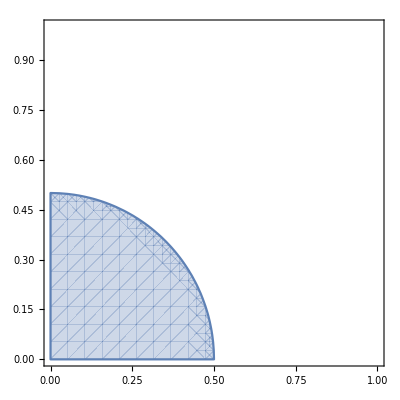
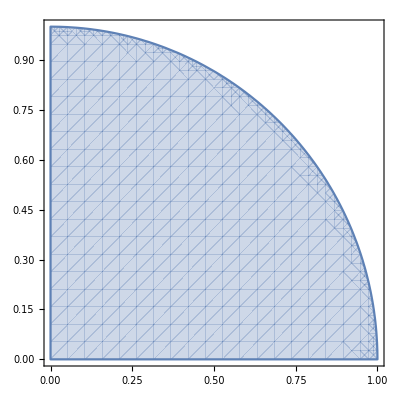
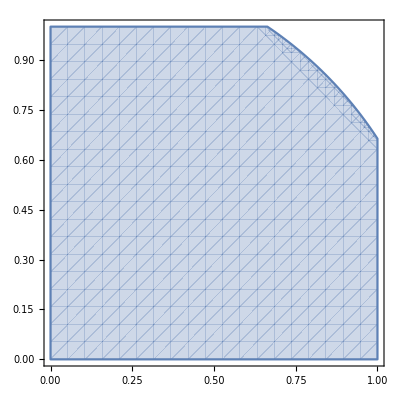
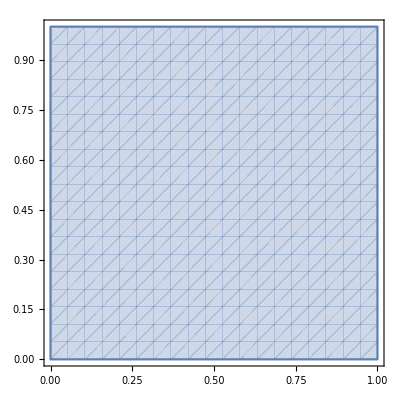
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
RegionPlot[x^2+y^2<=a^2&&a>=0,{x,0,1},{y,0,1}],
{a,{-1,0.5,1,1.2,2}}]
```

Вычислим площадь куска поверхности  z=xy, вырезанного цилиндром x^2+y^2=1

```mathematica
Clear[x,y,z]
ContourPlot3D[{z==x y, x^2+y^2==1},{x,-2,2},{y,-2,2},{z,-1,1},
Mesh->None,
ContourStyle->{
Directive[Orange,Opacity[0.8],Specularity[White,30]],
Directive[Blue,Opacity[0.5],Specularity[White,30]]
}]
```

-Graphics3D-

## Линейное (нелинейное) программирование

Рассмотрим задачу оптимизации выпуска изделий. Фирма выпускает два вида мороженного: сливочное и шоколадное. Для изготовления мороженного используется два исходных продукта: молоко и наполнители. Расходы на производство 1 кг мороженного и суточные запасы следующие:
- расход на производство 1 кг сливочного мороженного - 0.8 кг молока и 0.4 кг наполнителя;
- расход на производство 1 кг шоколадного мороженного - 0.4 кг молока и 0.8 кг наполнителя;
- суточный запас: 400 кг молока и 365 кг наполнителя.
Изучение рынка сбыта показало, что спрос на сливочное мороженное не превышает спрос на шоколадное более чем на 100кг в сутки. Кроме того, известно, что спрос на шоколадное мороженное не превышает 350кг в сутки. Розничная цена 1кг сливочного мороженного 60 руб., шоколадного 50 руб.
Какое количество мороженного каждого вида должна производить фирма, чтобы доход от реализации продукции был максимальным?

```mathematica
Maximize[{
60x1+50x2,
0.8x1+0.4x2<=400,
0.4x1+0.8x2<=365,
x1-x2<=100,
x2<=350,
x1>=0,x2>=0
},{x1,x2}]
```

{35500.,{x1→362.5,x2→275.}}

```mathematica
Maximize[{
60x1+50x2,
0.8x1+0.4x2<=400,
0.4x1+0.8x2<=365,
x1-x2<=100,
x2<=350,
x1>=0,x2>=0
},{x1,x2},Integers]
```

{35480.,{x1→363,x2→274}}